```mathematica
data = Import[NotebookDirectory[] <> "../data/btc future and reference rate/coingecko_future.csv"];
```

```mathematica
data[[1;;3]]
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
0 | 2021-02-03 | 37266.4 | 37790. | 0.0452987 | 0.0337738
1 | 2021-02-02 | 35615.9 | 36535. | 0.059664 | 0.0641463)

```mathematica
dates=Table[DateObject[data[[k,2]]], {k,2,Length[data]}];
```

```mathematica
Length[dates]
```

678

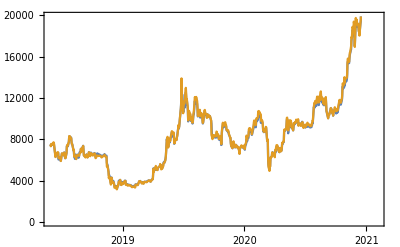

```mathematica
DateListPlot[{{dates,data[[2;;,3]]}ᵀ, {dates, data[[2;;,4]]}ᵀ}]
```

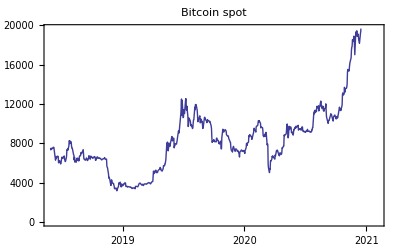

```mathematica
p1=DateListPlot[{dates,data[[2;;,3]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Bitcoin spot"]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_series.pdf", p1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_series.pdf

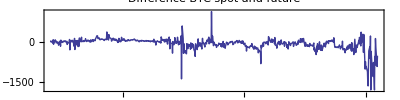

```mathematica
p2=DateListPlot[{dates,data[[2;;,3]]-data[[2;;,4]]}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"Difference BTC spot and future",PlotRange->All,AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_vs_future_series.pdf", p2]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_vs_future_series.pdf

```mathematica
r=data⟦2;;All,5⟧;
f=data⟦2;;All,6⟧;
sr=Sort[r];
m=Mean[r];
s=StandardDeviation[r];
l=Length[r];
```

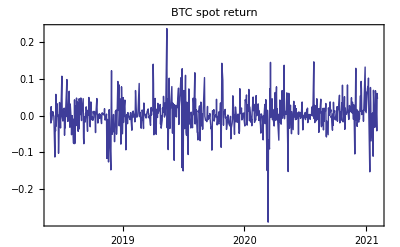

```mathematica
p3=DateListPlot[{dates,r}ᵀ,PlotTheme->"Classic",Joined->True,PlotStyle->Thick,PlotLabel->"BTC spot return",PlotRange->All]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_return_series.pdf", p3]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_return_series.pdf

```mathematica
extremes=Sort[Abs[r]][[-30;;]];
pos=Flatten[Table[Position[Abs[r],extremes[[k]]], {k,1,Length[extremes]}]];
```

```mathematica
p3a=DateListPlot[{dates[[pos]], r[[pos]]}ᵀ,PlotStyle->{Red,Thick},Joined->False];
```

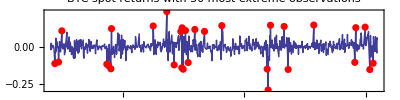

```mathematica
p3b=Show[p3,p3a, PlotLabel->"BTC spot returns with 30 most extreme observations",AspectRatio->1/4]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_series.pdf", p3b]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_series.pdf

```mathematica
NMaximize[{LogLikelihood[StudentTDistribution[ν], (r-m)/s],ν>2}, ν]
```

{-930.714,{ν→7.94508}}

Generalized Pareto distribution

```mathematica
K=Ceiling[l 0.05];
u=-sr⟦K⟧
```

0.0652943

```mathematica
y=-sr⟦1;;K-1⟧-u;
```

```mathematica
g[x_,β_,ξ_]:=1-(1+ξ x/β)^(-1/ξ)
```

```mathematica
NMaximize[{Total[Log[g[y,β,ξ]]],ξ>0&& β>0},{β,ξ}]
```

{0.,{β→6.58869×10^-8,ξ→0.203272}}

```mathematica
1/0.203272
```

4.91952

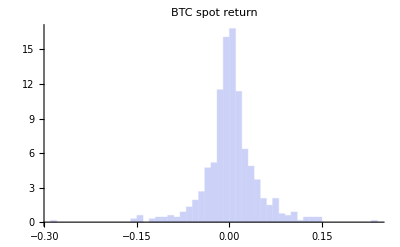

```mathematica
p4=Histogram[data[[2;;,5]],Automatic, "PDF", PlotTheme->"Classic", PlotLabel->"BTC spot return",PlotRange->All]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_hist.pdf", p4]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_hist.pdf

See gretl for summary statistics

```mathematica
t=Table[{InverseCDF[NormalDistribution[m,s],(k-0.5)/l],sr[[k]]}, {k,1,l}];
```

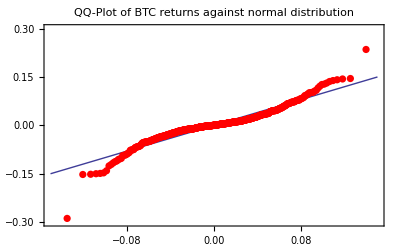

```mathematica
p5=Show[
Plot[x, {x,-0.15, 0.15},PlotTheme->"Classic",PlotRange->{-0.3,0.3}, Frame->True,PlotLabel->"QQ-Plot of BTC returns against normal distribution"],
ListPlot[t, PlotTheme->"Classic", PlotStyle->{Red, PointSize[0.013]},PlotRange->All]
]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_qq.pdf", p5]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_qq.pdf

Outliers are 3/2 times beyond the interquartile range; far outliers are beyond 3 times  the interquartile range.

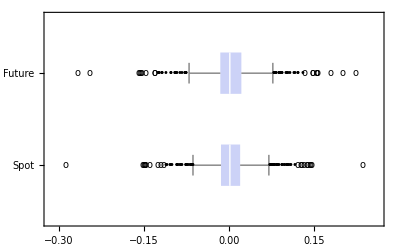

```mathematica
p6=BoxWhiskerChart[{r,f},{{"Outliers", "•"},{"FarOutliers", o}},PlotTheme->"Classic",  ChartLabels->{"Spot", "Future"},BarOrigin->Left]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_box.pdf", p6]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_box.pdf

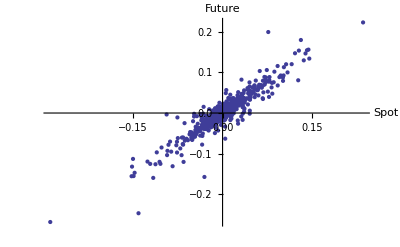

```mathematica
p7=ListPlot[{r,f}ᵀ,PlotTheme->"Classic",AxesLabel->{"Spot", "Future"},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_scatter.pdf", p7]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_scatter.pdf

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
usim=hatF[r];
vsim=hatF[f];
```

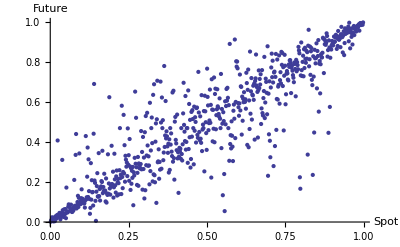

```mathematica
p8=ListPlot[{usim,vsim}ᵀ,PlotTheme->"Classic",AxesLabel->{"Spot", "Future"},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/btc_future_copula_scatter.pdf", p8]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/btc_future_copula_scatter.pdf

## Copula scatterplots

```mathematica
sp[dist_]:=12 NIntegrate[CDF[dist,{u,v}], {u,0,1}, {v,0,1}]-3
```

Gaussian copula / Spearman’s rho

```mathematica
sol=Solve[ 6/Pi ArcSin[1/2 ρ]==0.75,ρ]
```

{{ρ→0.765367}}

```mathematica
gaussian = CopulaDistribution[{"Binormal", ρ/.sol[[1]]}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[gaussian]
```

0.75

```mathematica
Plot3D[PDF[gaussian, {u,v}], {u,0,1}, {v,0,1},PlotTheme->"Classic"]
```

-Graphics3D-

```mathematica
r1=RandomVariate[gaussian, 1000];
```

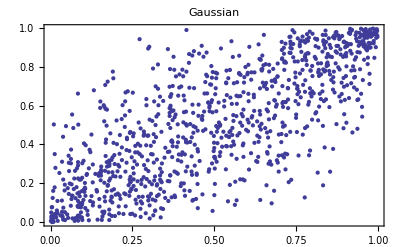

```mathematica
p1=ListPlot[r1,PlotTheme->"Classic", PlotStyle->Thick,Frame->True,PlotLabel->"Gaussian"]
```

Multivariate T

```mathematica
ρ=0.77025;StudentT=CopulaDistribution[{"MultivariateT", {{1,ρ}, {ρ,1}}, 10}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[StudentT]
```

0.749847

```mathematica
r2=RandomVariate[StudentT, 1000];
```

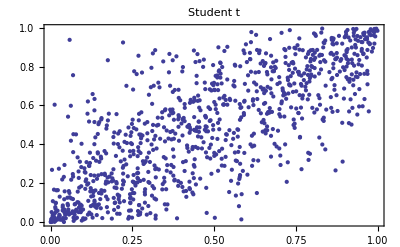

```mathematica
p2=ListPlot[r2,PlotTheme->"Classic", PlotStyle->Thick,Frame->True,PlotLabel->"Student t"]
```

Clayton

```mathematica
c=0.3875;
clayton = CopulaDistribution[{"Clayton", c}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[clayton]
```

0.75009

```mathematica
r3=RandomVariate[clayton, 1000];
```

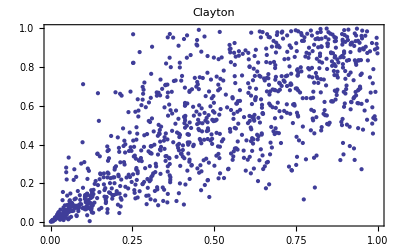

```mathematica
p3=ListPlot[r3,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Clayton"]
```

Frank

```mathematica
α=0.001199;
frank = CopulaDistribution[{"Frank", α}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[frank]
```

0.750022

```mathematica
r4=RandomVariate[frank, 1000];
```

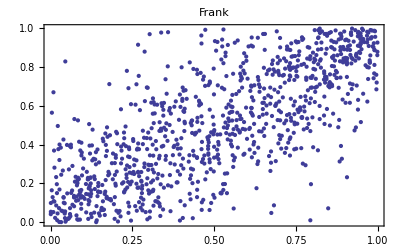

```mathematica
p4=ListPlot[r4,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Frank"]
```

Gumbel

```mathematica
α=2.2855;
gumbel=CopulaDistribution[{"GumbelHougaard", α}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[gumbel]
```

0.750056

```mathematica
r5=RandomVariate[gumbel, 1000];
```

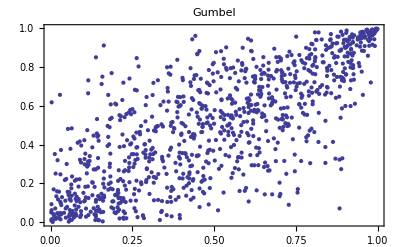

```mathematica
p5=ListPlot[r5,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Gumbel"]
```

Plackett
From Nelsen, p.99/100

From Nelsen, p. 171:

```mathematica
Clear[θ]
NSolve[0.75==(θ+1)/(θ-1)-(2 θ Log[θ])/(θ-1)^2,θ]
```

NSolve[0.75==(θ+1)/(θ-1)-(2 θ log(θ))/(θ-1)^2,θ]

```mathematica
sol=NMinimize[{(0.75-((θ+1)/(θ-1)-(2 θ Log[θ])/(θ-1)^2))^2,θ>0},{θ,15,20}]
```

{6.48932×10^-16,{θ→17.1395}}

```mathematica
θ=θ/.sol[[2]];
u=RandomVariate[UniformDistribution[],1000];
t=RandomVariate[UniformDistribution[],1000];
```

```mathematica
a=t (1-t);
b=θ+a (θ-1)^2;
c=2 a (u θ^2+1-u)+θ (1-2 a);
d=√θ √(θ+4 a u (1-u) (1-θ)^2);
v=(c-(1-2t )d)/(2 b);
```

```mathematica
r6 = {u,v}ᵀ;
```

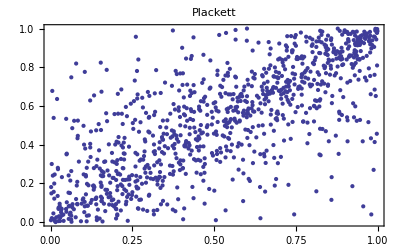

```mathematica
p6=ListPlot[r6,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Plackett"]
```

NIG factor model

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

```mathematica
α=1.5;
β=0.1;
Clear[δ]
```

Spearman Rho approximation of Gaussian

```mathematica
sol=NSolve[(6 ArcSin[δ/(2 δs[α,β])])/π==0.75, δ]
```

{{δ→1.14041}}

```mathematica
δ=δ/.sol⟦1⟧;
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
Y=RandomVariate[NormalDistribution[],{3,1000}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], 1000];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], 1000];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], 1000];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
```

```mathematica
SpearmanRho[X1,X2]
```

0.734809

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Timing[
usim = hatF[X1];
vsim = hatF[X2];
]
```

{0.043189,Null}

```mathematica
r7 = {usim,vsim}ᵀ;
```

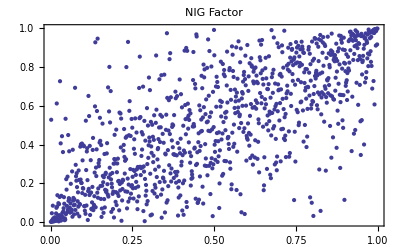

```mathematica
p7=ListPlot[r7,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"NIG Factor"]
```

Mixture copula

```mathematica
Clear[ρ,p]
```

```mathematica
p=0.8;
sol=Solve[ p 6/Pi ArcSin[1/2 ρ]==0.75,ρ]
```

{{ρ→0.942793}}

```mathematica
ρ=ρ/.sol[[1]]
```

0.942793

```mathematica
mixture = p CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}] + (1-p) CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
sp[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}]]
```

-8.88178×10^-16

```mathematica
p sp[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}]]
```

0.75

```mathematica
Plot3D[p PDF[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}],{u,v}]+ (1-p) PDF[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}],{u,v}], {u,0,1}, {v,0,1}]
```

-Graphics3D-

```mathematica
X=RandomVariate[NormalDistribution[],1000];
Z=RandomVariate[NormalDistribution[],1000];
W=RandomVariate[UniformDistribution[],1000];
```

```mathematica
Y=ConstantArray[0, 1000];
```

```mathematica
Table[If[W⟦k⟧≤p,Y⟦k⟧=ρ X⟦k⟧+√(1-ρ^2) Z⟦k⟧,Y⟦k⟧=Z⟦k⟧],{k,1,1000}];
```

```mathematica
Timing[
usim = hatF[X];
vsim = hatF[Y];
]
```

{0.043284,Null}

```mathematica
r8 = {usim,vsim}ᵀ;
```

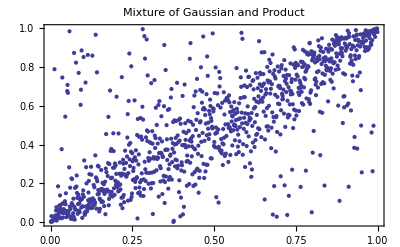

```mathematica
p8=ListPlot[r8,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Mixture of Gaussian and Product"]
```

```mathematica
p CDF[CopulaDistribution[{"Binormal", ρ}, {UniformDistribution[], UniformDistribution[]}],{u,v}]+ (1-p)CDF[CopulaDistribution["Product", {UniformDistribution[], UniformDistribution[]}],{u,v}]/.{u->.85, v->.65}
```

0.629627

```mathematica
Length[Select[{usim, vsim}ᵀ, #1[[1]]<=0.85 && #1[[2]]≤0.65&]]/1000.
```

0.633

```mathematica
Grid[{{p1, p2, p3, p4}, {},{p5, p6, p7, p8}}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/copulas_scatterplots.pdf", %]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/copulas_scatterplots.pdf

## h Parameters

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
hParams=Import[NotebookDirectory[] <> "../results/coingecko_future_v3/MM/OHR.csv"];
```

```mathematica
dates={};
For[k=0, k≤74, k++,
d=Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/"<> ToString[k] <> ".csv"];
AppendTo[dates,DateObject[d⟦2,2⟧]];
]
```

```mathematica
hParams[[1;;10]]
```

( | file_name | risk_measure | OHR | copula
0 | 73.csv | ERM k=10 | 0.920996 | Gaussian
1 | 73.csv | ES q=0.01 | 0.845898 | Gaussian
2 | 73.csv | ES q=0.05 | 0.914258 | Gaussian
3 | 73.csv | VaR q=0.01 | 0.928906 | Gaussian
4 | 73.csv | VaR q=0.05 | 0.957031 | Gaussian
5 | 73.csv | Variance | 0.907715 | Gaussian
6 | 36.csv | ERM k=10 | 0.872266 | Gaussian
7 | 36.csv | ES q=0.01 | 0.921973 | Gaussian
8 | 36.csv | ES q=0.05 | 0.88877 | Gaussian)

```mathematica
copulas=Union[hParams[[2;;,5]], {}];
measures=Union[hParams[[2;;,3]], {}];
```

```mathematica
measures
```

{ERM k=10,ES q=0.01,ES q=0.05,Variance,VaR q=0.01,VaR q=0.05}

```mathematica
measures={measures⟦4⟧,measures⟦5⟧,measures⟦6⟧,measures⟦2⟧,measures⟦3⟧,measures⟦1⟧}
```

{Variance,VaR q=0.01,VaR q=0.05,ES q=0.01,ES q=0.05,ERM k=10}

```mathematica
methods
```

{Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

```mathematica
hGaussian=Select[hParams, #1[[5]]=="Gaussian"&];
```

```mathematica
hGaussian[[1;;10]]
```

(0 | 73.csv | ERM k=10 | 0.920996 | Gaussian
1 | 73.csv | ES q=0.01 | 0.845898 | Gaussian
2 | 73.csv | ES q=0.05 | 0.914258 | Gaussian
3 | 73.csv | VaR q=0.01 | 0.928906 | Gaussian
4 | 73.csv | VaR q=0.05 | 0.957031 | Gaussian
5 | 73.csv | Variance | 0.907715 | Gaussian
6 | 36.csv | ERM k=10 | 0.872266 | Gaussian
7 | 36.csv | ES q=0.01 | 0.921973 | Gaussian
8 | 36.csv | ES q=0.05 | 0.88877 | Gaussian
9 | 36.csv | VaR q=0.01 | 0.85791 | Gaussian)

```mathematica
p={};
hFull={};
For[j=1, j≤Length[copulas], j++,
h={};
For[k=1, k≤Length[measures], k++,
htmp1=Select[hParams,#1⟦5⟧==copulas⟦j⟧&];
htmp=Select[htmp1,#1⟦3⟧==measures⟦k⟧&];
o=Ordering[ToExpression[StringReplace[htmp⟦1;;All,2⟧,".csv"->""]]];
AppendTo[h,htmp⟦o,4⟧];
];
AppendTo[p,DateListPlot[Table[Transpose[{dates,h⟦k⟧}],{k,1,Length[h]}],(*PlotLegends->measures,*)PlotLabel->copulas⟦j⟧,PlotRange->{0,1.2}]];
AppendTo[hFull, h];
]
```

Add NIG factor

```mathematica
hvec={};
For[j=0, j≤74, j++,
AppendTo[hvec, Import[NotebookDirectory[] <> "data/" <> ToString[j] <> "_h.csv"]];
(* order of risk measures: variance, VaR99, VaR95, ES99, ES95, Spectral10 *)
]
```

```mathematica
AppendTo[copulas, "NIG Factor"];
```

```mathematica
h={};
AppendTo[h,hvec[[;;,2]]];
AppendTo[h,hvec[[;;,3]]];
AppendTo[h,hvec[[;;,4]]];
AppendTo[h,hvec[[;;,5]]];
AppendTo[h,hvec[[;;,6]]];
AppendTo[h,hvec[[;;,7]]];
```

```mathematica
AppendTo[hFull,h[[;;,;;,1]]];
```

```mathematica
AppendTo[p,DateListPlot[Table[Transpose[{dates,h⟦k⟧}],{k,1,Length[h]}],(*PlotLegends->measures,*)PlotLabel->"NIG Factor",PlotRange->{0,1.2}]];
```

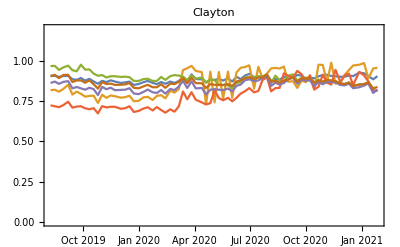
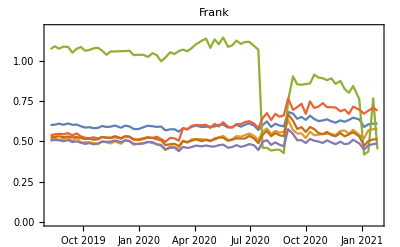
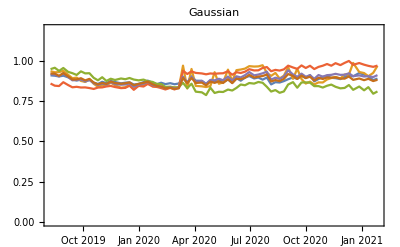
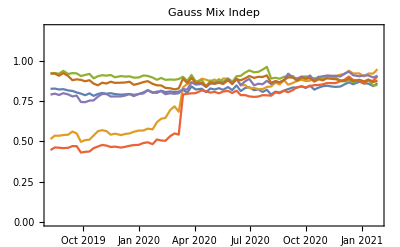
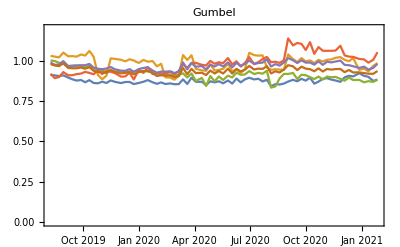
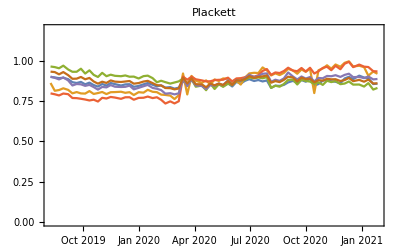
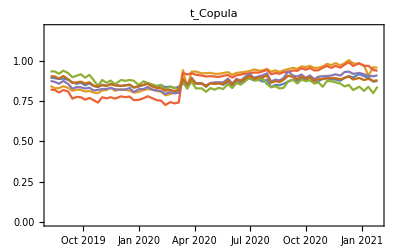
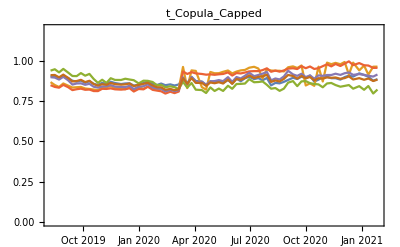

```mathematica
p
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/hParams_Legend.pdf",LineLegend[ColorData[97, "ColorList"],methods, LegendLayout->"Row"]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/hParams_Legend.pdf

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/hParams.pdf", Grid[{{p⟦3⟧,p⟦7⟧,p⟦1⟧,p⟦2⟧},{p⟦5⟧,p⟦6⟧,p⟦9⟧,p⟦4⟧}}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/hParams.pdf

## P&L

```mathematica
Dimensions[hFull]
```

{9,6,75}

```mathematica
Dimensions[hFull⟦1⟧]
```

{6,75}

h’s were generated with 30 days test in mind. For 100 days test, we need to discard data until 10 Sep 2020. 
Starting index:

```mathematica
dates⟦20⟧
```

Thu 10 Sep 2020

```mathematica
htmp=hFull[[9]];
```

```mathematica
htmp[[;;,20]]
```

{0.850481,0.888836,0.877198,0.875857,0.878191,0.848304}

### In-sample P&L

```mathematica
methods
measures
copulas
```

{Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

{Variance,VaR q=0.01,VaR q=0.05,ES q=0.01,ES q=0.05,ERM k=10}

{Clayton,Frank,Gaussian,Gauss Mix Indep,Gumbel,Plackett,t_Copula,t_Copula_Capped,NIG Factor}

```mathematica
For[ii=1, ii≤ Length[copulas], ii++,
htmp=hFull[[ii]];
For[kk=0, kk≤54, kk++,
data = (* in sample *)
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[20+kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,5⟧];
(* hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"]; *)
hvec=htmp[[;;,20+kk]];
PLdyn={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLstat={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PLdyn, PLbrr];
AppendTo[PLstat,Flatten[{"unhedged",Exp[Accumulate[rbrr]]}]];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PLdyn,PLbtc];
AppendTo[PLstat,Flatten[{"future", Exp[Accumulate[rbtc]]}]];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0; (* dynamic hedge; every day starts with h units of future *)
rh=Log[(1+PLh)];
PLs=Exp[Accumulate[rh]];
PrependTo[PLh, methods⟦jj⟧];
AppendTo[PLdyn, PLh];
PrependTo[PLs, methods⟦jj⟧];
AppendTo[PLstat, PLs];
PrependTo[rh, methods⟦jj⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<> copulas[[ii]] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<>copulas[[ii]]<> "_PLr_insample.csv",PLrᵀ]
]
]
```

### Out-of-sample P&L

```mathematica
For[ii=1, ii≤  Length[copulas], ii++,
htmp=hFull[[ii]];
For[kk=0, kk≤ 54, kk++,
data = (* out-of-sample *)
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v5/test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{data⟦k,2⟧,{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,6⟧];
brr=Reverse[data⟦2;;All,5⟧];
(*  hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];*)
hvec=htmp[[;;,20+kk]];
PLdyn={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLstat={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PLdyn, PLbrr];
AppendTo[PLstat,Flatten[{"unhedged",Exp[Accumulate[rbrr]]}]];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PLdyn,PLbtc];
AppendTo[PLstat,Flatten[{"future", Exp[Accumulate[rbtc]]}]];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=1, jj≤Length[hvec],jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PLs=Exp[Accumulate[rh]];
PrependTo[PLh, methods⟦jj⟧];
AppendTo[PLdyn, PLh];
PrependTo[PLs, methods⟦jj⟧];
AppendTo[PLstat, PLs];
PrependTo[rh, methods⟦jj⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<> copulas[[ii]] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_"<>copulas[[ii]]<> "_PLr_outsample.csv",PLrᵀ]
]
]
```

## P&L Plots

Which kind of P&L to look at? 
- 5 days (this would be daily return P&L, recalibrated as often as possible)
- 100 days (this would be the P&L of a static hedge, so only final P&L counts)

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

Out-of-sample (static)

```mathematica
d1[[1,2;;]]
```

{unhedged,future,Variance,VaR 99%,VaR 95%,ES 99%,ES 95%,Spectral 10}

```mathematica
dFull={};
For[ii=1, ii≤Length[copulas],ii++,
d={};
For[kk=0, kk≤54, kk++,
d1=Import[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_" <> copulas[[ii]]<> "_PLr_outsample.csv"];
If[kk==0,
d=Append[{d1[[1,2;;]]}, Exp[Total[d1[[2;;,2;;]]]]],
d=AppendTo[d,Exp[Total[d1[[2;;,2;;]]]]]
];
];
AppendTo[dFull, d];
]
```

```mathematica
Dimensions[dFull]
```

{9,56,8}

```mathematica
dFull[[1,1;;10]]//TableForm
```

unhedged | future | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
3.60305 | 3.6636 | 1.10865 | 1.14675 | 1.07991 | 1.11436 | 1.11173 | 1.10804
2.72914 | 2.78403 | 1.06267 | 1.10571 | 1.06005 | 1.06088 | 1.08748 | 1.08748
3.04684 | 3.08469 | 1.08804 | 1.00289 | 1.1212 | 1.05663 | 1.13844 | 1.11998
2.9733 | 2.99029 | 1.11959 | 1.02974 | 1.12392 | 1.18918 | 1.16162 | 1.14457
2.93876 | 3.00552 | 1.09291 | 1.00545 | 1.06505 | 1.16787 | 1.12128 | 1.10637
2.27349 | 2.32649 | 1.0709 | 0.995637 | 1.08501 | 1.13679 | 1.10276 | 1.07676
2.02446 | 1.98265 | 1.07242 | 1.06863 | 1.07289 | 1.08653 | 1.08009 | 1.07202
1.93953 | 1.89087 | 1.09151 | 1.09532 | 1.08412 | 1.10133 | 1.09173 | 1.08874
2.04651 | 2.05487 | 1.06223 | 1.01267 | 1.06133 | 1.13908 | 1.08283 | 1.06819

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p, BoxWhiskerChart[dFull[[ii,2;;]]ᵀ, ChartLabels->dFull[[ii,1]],PlotRange->{Automatic,Full},PlotTheme->"Classic", PlotLabel->copulas[[ii]]]];
]
```

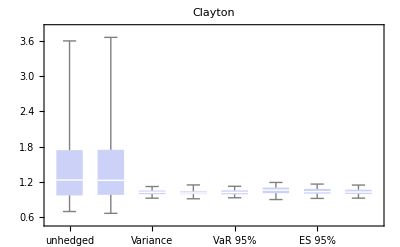
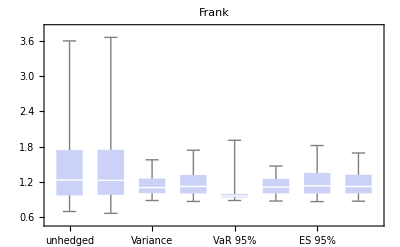
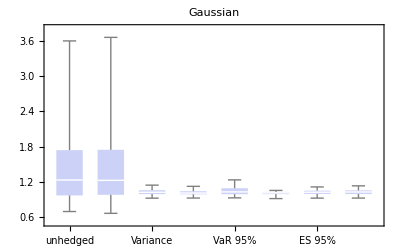
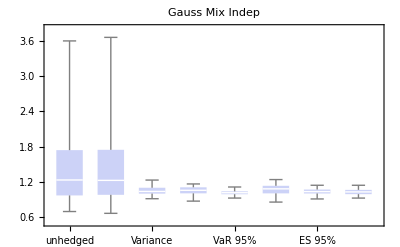
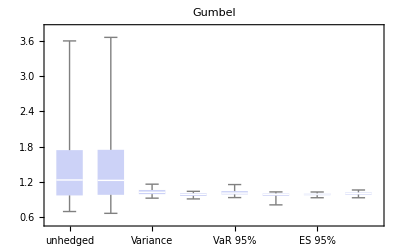
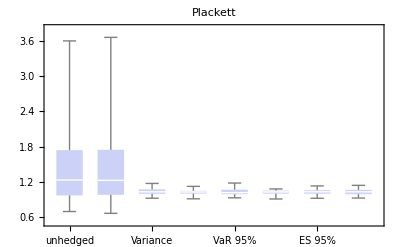
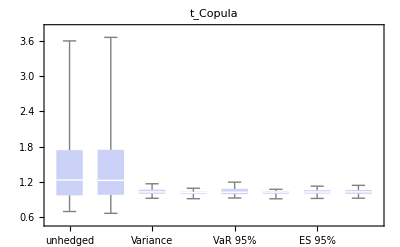
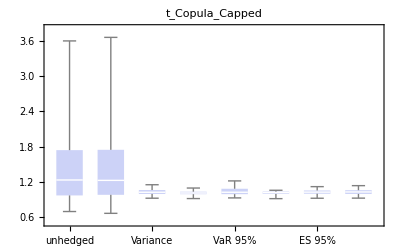

```mathematica
p
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/PL_static_out_tcop.pdf",p[[7]]];
```

```mathematica
p={};
For[ii=1, ii<=Length[copulas], ii++,
AppendTo[p,  BoxWhiskerChart[dFull⟦ii,2;;All,3;;All⟧ᵀ, (*ChartLabels->dFull[[ii,1,3;;]],*)PlotRange->{Automatic,{0.8,2}},PlotTheme->"Classic", PlotLabel->copulas⟦ii⟧]];
]
```

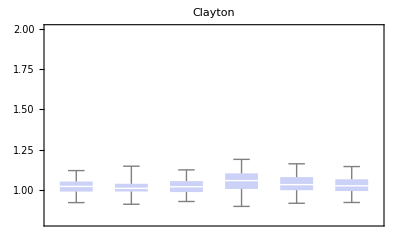
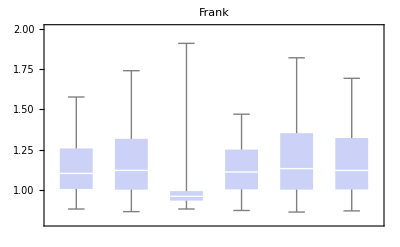
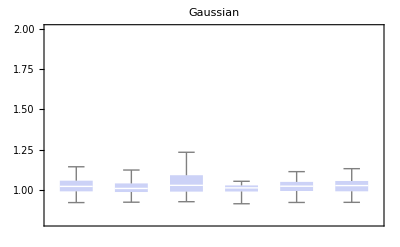
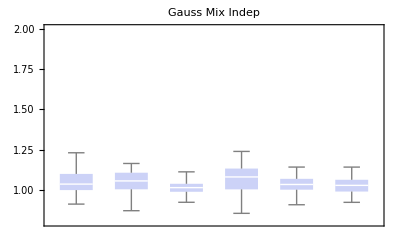
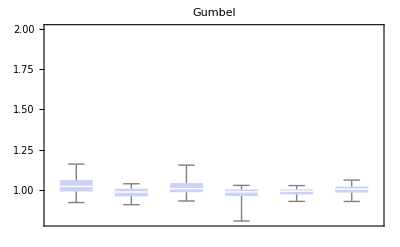
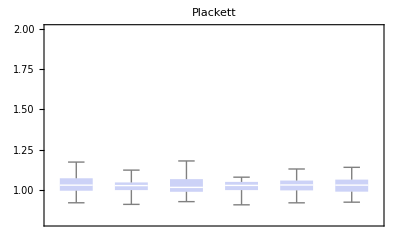
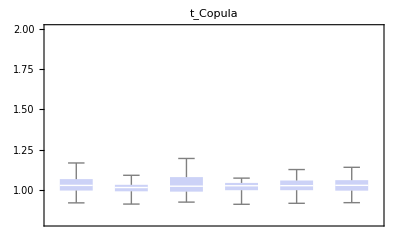
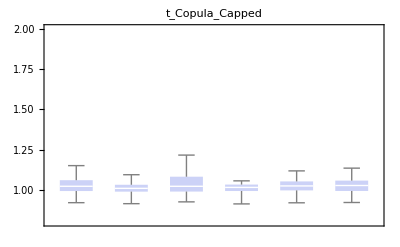

```mathematica
p
```

```mathematica
Export[NotebookDirectory[]<> "../latex/_pics/PL_static_out.pdf", Grid[{{p⟦3⟧,p⟦7⟧,p⟦1⟧,p⟦2⟧},{p⟦5⟧,p⟦6⟧,p⟦9⟧,p⟦4⟧}}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/PL_static_out.pdf

Out-of-sample (dynamic)

```mathematica
dFull={};
For[ii=1, ii≤Length[copulas],ii++,
d={};
For[kk=0, kk≤54, kk++,
d1=Import[NotebookDirectory[] <> "data_PL/" <> ToString[kk] <> "_" <> copulas[[ii]]<> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1⟦2;;All⟧]
];
];
AppendTo[dFull, d];
]
```

```mathematica
Dimensions[dFull]
```

{9,5501,9}

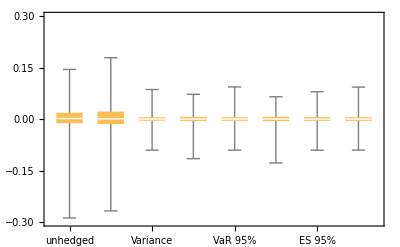

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

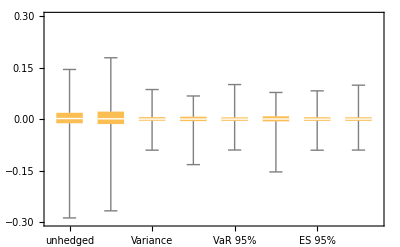

```mathematica
BoxWhiskerChart[dFull[[4,2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

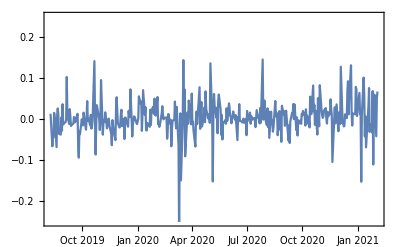
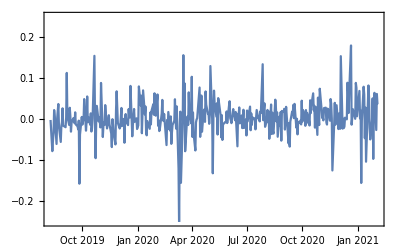

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

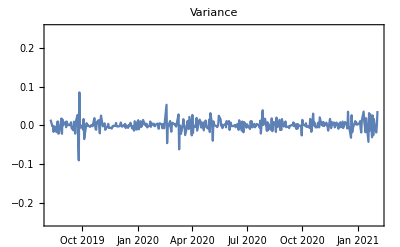
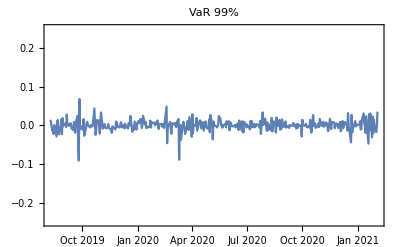
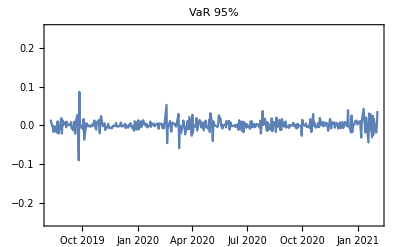
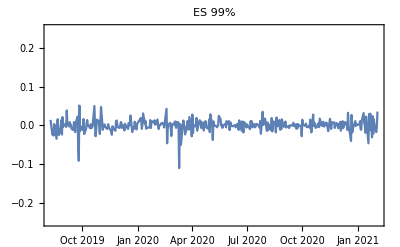
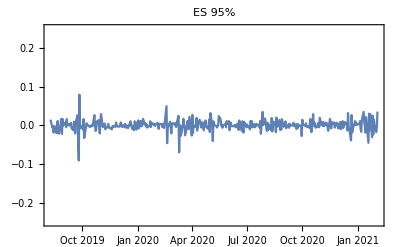
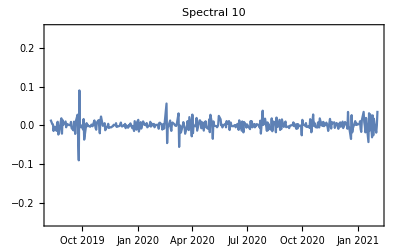

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤74, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

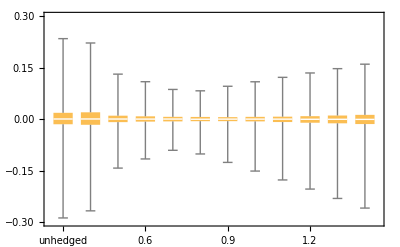

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤74, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

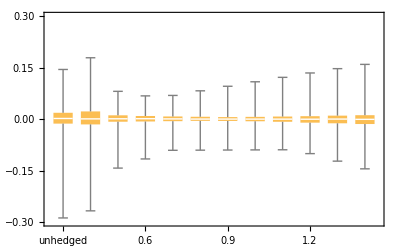

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤74, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-01-27 | 0.861697 | 0.90724 | 0.858251 | 0.90097 | 0.900107 | 0.845874
2021-01-20 | 0.858795 | 0.911378 | 0.872091 | 0.902477 | 0.87855 | 0.8555
2021-01-12 | 0.864889 | 0.917111 | 0.88249 | 0.906657 | 0.891102 | 0.871234
2021-01-05 | 0.854877 | 0.913529 | 0.76534 | 0.903447 | 0.867469 | 0.8658
2020-12-28 | 0.857776 | 0.913705 | 0.787804 | 0.902536 | 0.874686 | 0.872473
2020-12-18 | 0.87334 | 0.930919 | 0.804835 | 0.914826 | 0.906892 | 0.888932
2020-12-11 | 0.868997 | 0.925976 | 0.812892 | 0.91115 | 0.922375 | 0.877076
2020-12-04 | 0.865124 | 0.921301 | 0.791471 | 0.909374 | 0.908767 | 0.861755
2020-11-27 | 0.852697 | 0.913878 | 0.867317 | 0.904849 | 0.882367 | 0.845002
2020-11-19 | 0.849299 | 0.90704 | 0.869951 | 0.889571 | 0.867008 | 0.884744
2020-11-12 | 0.849971 | 0.913078 | 0.860374 | 0.902701 | 0.865418 | 0.876136
2020-11-05 | 0.85058 | 0.905246 | 0.865706 | 0.893152 | 0.86412 | 0.856505
2020-10-29 | 0.848182 | 0.904067 | 0.864617 | 0.890662 | 0.86353 | 0.884328
2020-10-22 | 0.845546 | 0.90239 | 0.868436 | 0.892626 | 0.869814 | 0.831041
2020-10-15 | 0.843691 | 0.899063 | 0.860168 | 0.88176 | 0.863882 | 0.877743
2020-10-08 | 0.842406 | 0.894889 | 0.859429 | 0.882811 | 0.855451 | 0.856438
2020-10-01 | 0.841612 | 0.896913 | 0.86403 | 0.883525 | 0.8577 | 0.82818
2020-09-24 | 0.840848 | 0.895922 | 0.859813 | 0.883102 | 0.874074 | 0.833981
2020-09-17 | 0.844579 | 0.885178 | 0.891271 | 0.865494 | 0.857726 | 0.852007
2020-09-10 | 0.850481 | 0.888836 | 0.877198 | 0.875857 | 0.878191 | 0.848304
2020-09-02 | 0.840246 | 0.876125 | 0.882629 | 0.866487 | 0.934327 | 0.840598
2020-08-26 | 0.824932 | 0.87355 | 0.82391 | 0.861045 | 0.845409 | 0.868543
2020-08-19 | 0.822652 | 0.870228 | 0.824558 | 0.857678 | 0.844088 | 0.820169
2020-08-12 | 0.822185 | 0.871797 | 0.826383 | 0.860947 | 0.842921 | 0.853373
2020-08-05 | 0.820589 | 0.858025 | 0.830879 | 0.847639 | 0.851604 | 0.822155
2020-07-29 | 0.81824 | 0.853119 | 0.816692 | 0.843876 | 0.856601 | 0.831521
2020-07-22 | 0.814721 | 0.854317 | 0.828292 | 0.843508 | 0.844749 | 0.82222
2020-07-15 | 0.827084 | 0.852875 | 0.82474 | 0.837347 | 0.845228 | 0.846115
2020-07-08 | 0.829067 | 0.853094 | 0.819165 | 0.843055 | 0.848795 | 0.84001
2020-06-30 | 0.826314 | 0.862666 | 0.815123 | 0.837724 | 0.851489 | 0.836331
2020-06-23 | 0.82877 | 0.853423 | 0.821308 | 0.841384 | 0.84998 | 0.835112
2020-06-16 | 0.828245 | 0.85574 | 0.823728 | 0.842806 | 0.848206 | 0.834655
2020-06-09 | 0.834062 | 0.854317 | 0.819879 | 0.842253 | 0.847153 | 0.837461
2020-06-02 | 0.835757 | 0.861201 | 0.819356 | 0.844115 | 0.850387 | 0.845986
2020-05-26 | 0.83398 | 0.854163 | 0.820762 | 0.841062 | 0.847153 | 0.837845
2020-05-18 | 0.833287 | 0.853261 | 0.810048 | 0.841342 | 0.8518 | 0.867202
2020-05-11 | 0.829956 | 0.851042 | 0.806006 | 0.83901 | 0.853 | 0.838499
2020-05-04 | 0.823955 | 0.853333 | 0.819185 | 0.841515 | 0.818771 | 0.862866
2020-04-27 | 0.822995 | 0.857032 | 0.823769 | 0.846807 | 0.822326 | 0.853781
2020-04-20 | 0.820754 | 0.856948 | 0.825054 | 0.843975 | 0.819676 | 0.848764
2020-04-13 | 0.821398 | 0.85439 | 0.818352 | 0.842777 | 0.818481 | 0.849924
2020-04-03 | 0.821491 | 0.863412 | 0.832842 | 0.844942 | 0.827655 | 0.846761
2020-03-27 | 0.825828 | 0.859913 | 0.834751 | 0.847845 | 0.829055 | 0.847829
2020-03-20 | 0.824868 | 0.860413 | 0.834896 | 0.848702 | 0.827301 | 0.866636
2020-03-13 | 0.822037 | 0.86279 | 0.843413 | 0.842939 | 0.815445 | 0.867822
2020-03-06 | 0.811195 | 0.704645 | 0.823581 | 0.621813 | 0.780104 | 0.836097
2020-02-28 | 0.816288 | 0.753143 | 0.809962 | 0.67609 | 0.768865 | 0.88236
2020-02-21 | 0.814043 | 0.725311 | 0.817544 | 0.62803 | 0.743435 | 0.851586
2020-02-13 | 0.821999 | 0.740424 | 0.818965 | 0.641684 | 0.756265 | 0.876074
2020-02-06 | 0.821332 | 0.733882 | 0.81587 | 0.593586 | 0.753381 | 0.891839
2020-01-30 | 0.821653 | 0.688618 | 0.816223 | 0.647105 | 0.791251 | 0.875859
2020-01-23 | 0.817346 | 0.679859 | 0.818938 | 0.587119 | 0.779738 | 0.865258
2020-01-15 | 0.816373 | 0.677122 | 0.816259 | 0.584602 | 0.778229 | 0.86489
2020-01-08 | 0.811856 | 0.662963 | 0.820164 | 0.576881 | 0.776586 | 0.864685
2019-12-31 | 0.812149 | 0.630884 | 0.816266 | 0.563908 | 0.781206 | 0.880043
2019-12-23 | 0.811273 | 0.707861 | 0.82022 | 0.609007 | 0.766925 | 0.845084
2019-12-16 | 0.811195 | 0.603236 | 0.824025 | 0.586317 | 0.767106 | 0.831247
2019-12-09 | 0.810073 | 0.707307 | 0.818201 | 0.61013 | 0.767387 | 0.835988
2019-12-02 | 0.810592 | 0.707933 | 0.819998 | 0.608718 | 0.768485 | 0.836737
2019-11-22 | 0.810436 | 0.656938 | 0.817182 | 0.602307 | 0.769755 | 0.837863
2019-11-15 | 0.808218 | 0.641451 | 0.808933 | 0.567836 | 0.775327 | 0.875486
2019-11-08 | 0.812159 | 0.650852 | 0.816485 | 0.584812 | 0.766364 | 0.832547
2019-11-01 | 0.810591 | 0.668919 | 0.820405 | 0.600625 | 0.767235 | 0.840272
2019-10-25 | 0.807289 | 0.717291 | 0.819772 | 0.555905 | 0.764634 | 0.833162
2019-10-18 | 0.798381 | 0.643704 | 0.833641 | 0.603867 | 0.751055 | 0.833717
2019-10-11 | 0.803767 | 0.693326 | 0.826963 | 0.529114 | 0.754048 | 0.836589
2019-10-04 | 0.804308 | 0.623393 | 0.831696 | 0.549276 | 0.75497 | 0.82978
2019-09-27 | 0.803612 | 0.640053 | 0.832699 | 0.548825 | 0.753678 | 0.830403
2019-09-20 | 0.81678 | 0.690169 | 0.827488 | 0.566893 | 0.773281 | 0.855722
2019-09-13 | 0.823324 | 0.680435 | 0.816096 | 0.583995 | 0.773281 | 0.860017
2019-09-06 | 0.819143 | 0.725158 | 0.830354 | 0.591004 | 0.768244 | 0.855422
2019-08-29 | 0.825167 | 0.668269 | 0.829651 | 0.578349 | 0.771902 | 0.874596
2019-08-22 | 0.825094 | 0.68377 | 0.885605 | 0.577836 | 0.772734 | 0.864916
2019-08-15 | 0.82891 | 0.640981 | 0.819281 | 0.54138 | 0.780141 | 0.882039
2019-08-08 | 0.825166 | 0.66628 | 0.817855 | 0.543133 | 0.779037 | 0.89456)

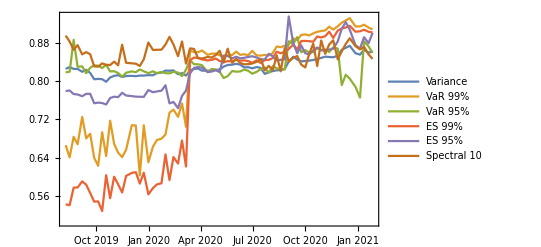

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods]
```